```mathematica
MHz=10^6;GHz=10^9;mm=10^(-3);

Γ=2*Pi*6.06MHz; (*Natural linewidth*)
Isat=30.5; (*Saturation intencity in SI units- linearly polarized light*)
Δ = 100GHz;  (*Detuning of laser*)

r=30mm;   (*Beam waist*)
P1=5;  (*Power*)
P2=5;
I1 = P1/(4*Pi*r*r); (*Intensity*)
I2 = P2/(4*Pi*r*r);
Subscript[Ω, eff][I1_,I2_,Δ_]=Γ(((I1/Isat)*(I2/Isat))^0.5)/(4*(Δ/Γ)) (*Rabi frequency*)

Subscript[τ, half][I1_,I2_,Δ_]=(10^6)Pi*0.5/Subscript[Ω, eff][I1,I2,Δ] (*pi/2 pulse timing in μs*)
Subscript[τ, pi][I1_,I2_,Δ_]=(10^6)Pi/Subscript[Ω, eff][I1,I2,Δ](*pi pulse timing in μs*)
```

52536.7

29.899

59.7981

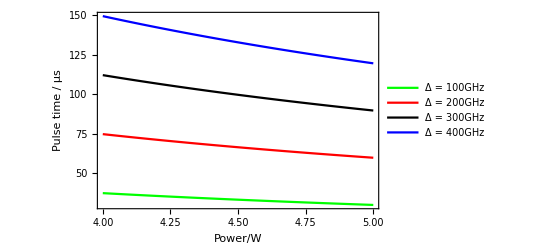

9-21-22-10.png

```mathematica
ClearAll[I2,Δ,I1]
Subscript[Ω, eff][I1_,I2_,Δ_]=Γ(((I1/Isat)*(I2/Isat))^0.5)/(4*(Δ/Γ)); (*Rabi frequency*)
p1=Plot[(10^6)Pi*0.5/Subscript[Ω, eff][i/(4*Pi*r*r),i/(4*Pi*r*r),100GHz],{i,4,5},Frame->True,FrameLabel->{"Power/W","Pulse time / μs"},PlotStyle->Green,PlotLegends->{"Δ = 100GHz"},PlotRange->All];
p2=Plot[(10^6)Pi*0.5/Subscript[Ω, eff][i/(4*Pi*r*r),i/(4*Pi*r*r),200GHz],{i,4,5},Frame->True,FrameLabel->{"Power/W","Pulse time / μs"},PlotStyle->Red,PlotLegends->{"Δ = 200GHz"},PlotRange->All];
p3=Plot[(10^6)Pi*0.5/Subscript[Ω, eff][i/(4*Pi*r*r),i/(4*Pi*r*r),300GHz],{i,4,5},Frame->True,FrameLabel->{"Power/W","Pulse time / μs"},PlotStyle->Black,PlotLegends->{"Δ = 300GHz"},PlotRange->All];
p4=Plot[(10^6)Pi*0.5/Subscript[Ω, eff][i/(4*Pi*r*r),i/(4*Pi*r*r),400GHz],{i,4,5},Frame->True,FrameLabel->{"Power/W","Pulse time / μs"},PlotStyle->Blue,PlotLegends->{"Δ = 400GHz"},PlotRange->All];
Show[p1,p2,p3,p4]
Export["9-21-22-10.png",Show[p1,p2,p3,p4]]
```

```mathematica
g=9.8;
height=11.6;
time=10;
ts=0.5;
drop[h_,t_,ts_]=height-0.5*g*(t+ts)*(t+ts);
dropdata=Table[i+j,{i,0,height,height/10},{j,0,time-1,time/10}]
ListPlot[dropdata]
ListLinePlot[dropdata,DataRange->{0,time-1},PlotStyle->{{Red,Dashing[Large]}},PlotRangeClipping->False,Ticks->{Automatic,Automatic}]
```

```mathematica
tbl={{1,2,3,4},{2,5,7,8},{9,10,11,12}}
x=tbl[[All,1]]
y=tbl[[All,4]]
data=Transpose[{x,y,x}]
ListLinePlot[data,Mesh->All,AxesOrigin->{0,0}]
```

```mathematica
For[i=0,i<2,i++,
If[]

]
```

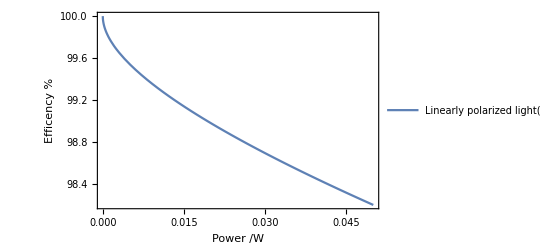

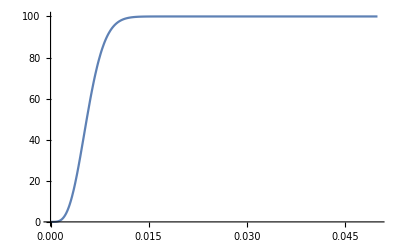

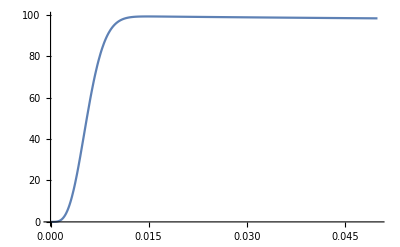

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=16.5 ;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=0;
detuning=300GHz;
radius=(0.0001/(4*Pi))^0.5;
n=2;
acctime=1ms;

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,theta]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);

Finalpower=0.05;
p1=Plot[100*(Subscript[F, sp][P,detuning,radius,theta,acctime]),{P,0,Finalpower},PlotRange->All,Frame->True,FrameLabel->{"Power /W","Efficency %"},PlotLegends->{"Linearly polarized light(I_sat=30.6 W/m^2)"}]
Plot[100*(Subscript[F, LZ][n,P,detuning,acctime,radius]),{P,0,Finalpower},PlotRange->All]
Plot[100*(Ftot[P,detuning,radius,0,acctime,n,radius]),{P,0,Finalpower},PlotRange->All]
```

```mathematica
Vo[P,detuning,radius]
A[radius]
 ℏ
Γ
((P/(A[r]))/Subscript[I, sat])
((Δ/Γ)*Er)
```

(7.9913×10^-29 P)/(ⅇ_(1/200))

π/10000

1.05457×10^-34

3.81075×10^7

(0.0026091 P)/r^2

2.62449×10^-37 Δ

```mathematica
Stanford
```

General::munfl: 0.0000771249^2500 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.16587×10^-6)^2500 is too small to represent as a normalized machine number; precision may be lost.

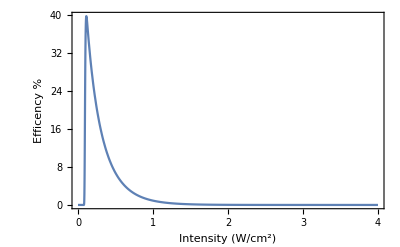

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=16.56;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=29*Pi/180;
detuning=2*Pi*91GHz;
radius=1.5mm;
n=2500;
acctime=29 ms;

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);

Finalpower=4;
p1=Plot[100*(Subscript[F, sp][P,detuning,radius,theta,acctime]),{P,0,Finalpower},PlotRange->All,Frame->True,FrameLabel->{"Power /W","Efficency %"},PlotLegends->{"circularly polarized light(I_sat=30.6 W/m^2)"}];
Plot[100*(Subscript[F, LZ][n,P,detuning,acctime,radius]),{P,0,Finalpower},PlotRange->All];
Plot[100*(Ftot[P*A[radius]*10^4,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Intensity (W/cm^2)","Efficency %"}]
```

```mathematica
-
```

```mathematica
4*Pi*1.5mm*1.5mm*4*10^4
```

1.13097

```mathematica
m*13/(2*k*ℏ)
```

1104.2

General::munfl: (1.37818×10^-7)^200 is too small to represent as a normalized machine number; precision may be lost.

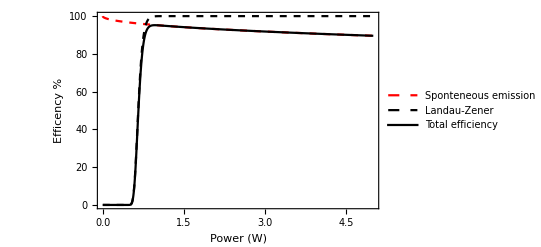

9-22-22-16.png

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P,Δ,nm,MHz,GHz,nm,ms,λ,Γ,k,ℏ,m,Er,ωr,τ,α]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=30.5;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=0;
detuning=300GHz;
radius=5mm;
n=200;
acctime=10 ms;

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);

Finalpower=5;
p1=Plot[100*(Subscript[F, sp][P,detuning,radius,theta,acctime]),{P,0,Finalpower},PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Sponteneous emission"},PlotStyle->{Red,Dashed}];
p2=Plot[100*(Subscript[F, LZ][n,P,detuning,acctime,radius]),{P,0,Finalpower},PlotRange->All,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Landau-Zener"},PlotStyle->{Black,Dashed}];
p3=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Total efficiency"},PlotStyle->{Black,Thick}];
Show[p1,p2,p3]
Export["9-22-22-16.png",Show[p1,p2,p3]]
```

```mathematica
Diffrent detuning
```

General::munfl: (1.69655×10^-10)^1200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.48272×10^-10)^1200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.69654×10^-9)^1200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.48272×10^-9)^1200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.69654×10^-8)^1200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.54482×10^-8)^1200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.08963×10^-8)^1200 is too small to represent as a normalized machine number; precision may be lost.

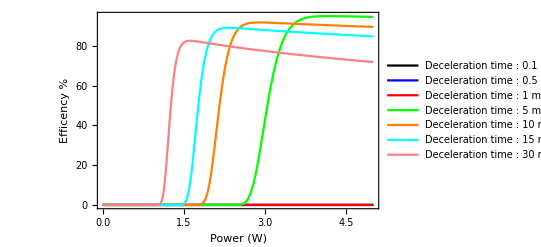

9-22-22-34.png

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=30.5;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;
vint = 5;
ω0 = k*vint;
theta=0;
detuning=300GHz;
radius=5mm;
n=1200;
acctime=10 ms;

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=(ω0+No*ωr)/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);


Finalpower=5;
acctime=0.1 ms;
p1=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Deceleration time : 0.1 ms "},PlotStyle->{Black,Thick}];

acctime=0.5 ms;
p2=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Deceleration time : 0.5 ms "},PlotStyle->{Blue,Thick}];
acctime=1 ms;
p3=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Deceleration time : 1 ms "},PlotStyle->{Red,Thick}];
acctime=5 ms;
p4=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Deceleration time : 5 ms "},PlotStyle->{Green,Thick}];
acctime=10 ms;
p5=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Deceleration time : 10 ms "},PlotStyle->{Orange,Thick}];
acctime=15 ms;
p6=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Deceleration time : 15 ms "},PlotStyle->{Cyan,Thick}];
acctime=30 ms;
p7=Plot[100*(Ftot[P,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Power (W)","Efficency %"},PlotLegends->{"Deceleration time : 30 ms "},PlotStyle->{Pink,Thick}];

Show[p1,p2,p3,p4,p5,p6,p7]
Export["9-22-22-34.png",Show[p1,p2,p3,p4,p5,p6,p7]]
```

General::munfl: (1.74107×10^-7)^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.83534×10^-7)^200 is too small to represent as a normalized machine number; precision may be lost.

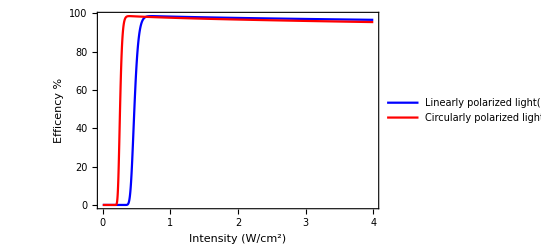

9-22-22-12.png

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=16.56;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=0;
detuning=400GHz;
radius=1.5mm;
n=200;
acctime=2 ms;

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);

Finalpower=4;
detuning=300GHz;
Subscript[I, sat]=30.5;
Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);
p1=Plot[100*(Ftot[P*A[radius]*10^4,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Intensity (W/cm^2)","Efficency %"},PlotLegends->{"Linearly polarized light(I_sat=30.6 W/m^2)"},PlotStyle->{Blue,Thick}];
Subscript[I, sat]=16.66;
Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);
p2=Plot[100*(Ftot[P*A[radius]*10^4,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Intensity (W/cm^2)","Efficency %"},PlotLegends->{"Circularly polarized light(I_sat=16.6 W/m^2)"},PlotStyle->{Red,Thick}];
Show[p1,p2]
Export["9-22-22-12.png",Show[p1,p2]]
```

FindMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMaxValue::nrnum: The function value -100 ⅇ^(-0.000076792 acct) (1-ⅇ^(-2.48767×10^-7 acct))^200 is not a real number at {P} = {0.0001}.

General::stop: Further output of FindMaxValue::nrnum will be suppressed during this calculation.

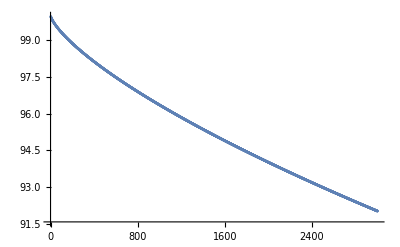

General::munfl: (3.32214×10^-8)^200 is too small to represent as a normalized machine number; precision may be lost.

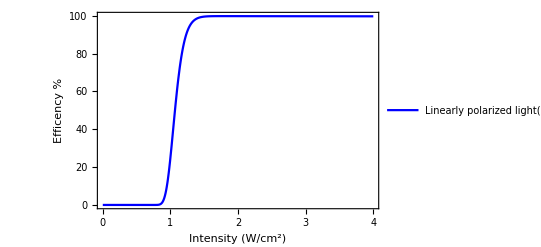

```mathematica
ClearAll[No,A,r,Vo,n,θ,theta,P]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A[r_]=4*Pi*r*r; (*Area*)
Subscript[I, sat]=16.56;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=0;
detuning=400GHz;
radius=1.5mm;
n=200;
acctime=0.2 ms;

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A[r]*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A[r]/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,θ]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]= ℏ*Γ*0.5*((P/(A[r]))/Subscript[I, sat])/((Δ/Γ)*Er);
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r]);
ListPlot[Table[FindMaxValue[100*(Ftot[P*A[radius]*10^4,detuning,radius,theta,acct/1000,n,radius]),{P,0.0001,1}],{acct,0,30,0.01}],PlotRange->All]
Plot[100*(Ftot[P*A[radius]*10^4,detuning,radius,theta,acctime,n,radius]),{P,0,Finalpower},PlotRange->All,PlotRange->All,Frame->True,FrameLabel->{"Intensity (W/cm^2)","Efficency %"},PlotLegends->{"Linearly polarized light(I_sat=30.6 W/m^2)"},PlotStyle->{Blue,Thick}]
```

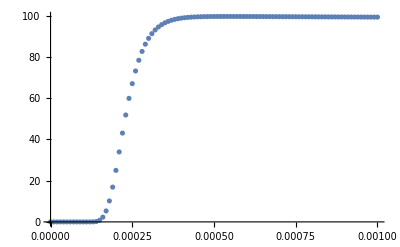

```mathematica
tbl={{1,2,3,4},{2,5,7,8},{9,10,11,12}};
y=Table[100*(Ftot[1*A[radius]*10^4,detuning,radius,theta,acct/1000,n,radius]),{acct,0,1,0.01}];
x=Table[acct/1000,{acct,0,1,0.01}];
data=Transpose[{x,y}];
ListPlot[data,PlotRange->All]
```